### symbolic inversion

```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A/ρ*kx/ω*Exp[k*z]-B/ρ*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A/ρ*ky/ω*Exp[k*z]-B/ρ*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A/ρ*k/ω*Exp[k*z]-I*B/ρ*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=-ρ*g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
subs1={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2]};
subs2={kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) kx)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) ky)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω)+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))-g z ρ

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]/ρ]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]/ρ]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]/ρ+g]
```

0

0

0

```mathematica
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs1/.subs2],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs1/.subs2],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,4]*I2m[l1,m1,m2,n1,n2])-kx/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,6]*I2m[l1,m1,m2,n1,n2])-ky/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,8]*I2m[l1,m1,m2,n1,n2])+I*k/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]-KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2]},{k1,1,9}]];
```

```mathematica
elim=Range[6];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Expand[Det[eqs1[[elim,perts[[i]]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;Abs[u]≠0.]]
ipert=lperts[[7]]
First/@subs1[[Complement[Range[9],perts[[ipert]]]]]
```

{2,3,4,5,7,8,9,10,11,12,13,14,18,19,20,21,24,25,26,27}

9

{Bx,By,H}

```mathematica
mat=FullSimplify[Expand[FullSimplify[Simplify[eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]/.m2->m1/.n2->n1/.l2->l1].(eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.m2->m1/.n2->n1/.l2->l1)/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ(ρ/μ*Ω1[n1,m1,l1]-κx^2-κy^2)-l1 ωd/.κx^2->κ1[n1,m1]^2-κy^2,κ1[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ1[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l2->l1].DiagonalMatrix[{ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ρ}]]/.I2m[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2])/2/ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))/.I2p[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2])/2/ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))/.I1m[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]+S1[m1,m2,n1,n2])/2/ⅇ^(h0 κ1[n1,m1])/.I1p[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]-S1[m1,m2,n1,n2])/2/ⅇ^(-h0 κ1[n1,m1])]/.-κ1[n1,m1]^2+κy[n1,m1]^2->-κx[n1,m2]^2;
MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]
```

(C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κx[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κx[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κy[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κy[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
(ⅈ S2[l1,m1,m2,n1,n2] κx[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | (ⅈ S2[l1,m1,m2,n1,n2] κy[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -μ C2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+μ S2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+1/2 C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+(S1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))

```mathematica
FullSimplify[MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]/.κ[n1,m1]->Subscript[κ,m n]/.Ω1[n1,m1,l1]->Subscript["Ω",l m n]/.κx[n1,m1]->Subscript[κx,m n]/.κy[n1,m1]->Subscript[κy,m n]/.C1[m1,m2,n1,n2]->Subsuperscript[C1,m'n',m n]/.S1[m1,m2,n1,n2]->Subsuperscript[S1,m' n',m n]/.C2[l1,m1,m2,n1,n2]->Subsuperscript[C2,l'm'n',l m n]/.S2[l1,m1,m2,n1,n2]->Subsuperscript[S2,l'm'n',l m n]]
```

(C2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κx[n1,m2]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κx_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
-(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | C2_(l' m' n')^(l m n)-(2 μ κy_(m n)^2 C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κy_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
ⅈ κx_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | ⅈ κy_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | 1/2 (ρ Ω_(l m n) C1_(m' n')^(m n)+κ1[n1,m1] (μ (C1_(m' n')^(m n)-2 C2_(l' m' n')^(l m n)+2 S2_(l' m' n')^(l m n)) κ1[n1,m1]+(S1_(m' n')^(m n) (g ρ^2+(ρ σ-4 μ^2 √((ρ Ω_(l m n))/μ)) κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2))))

### flat substrate

```mathematica
Ω1[l1_]:=((qx^2+qy^2)+I*ρ/μ*(ω+l1*ωd))^(1/2)
κ=(qx^2+qy^2)^(1/2);
mat1flat[l1_,l2_]:={{2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]+(2 (qy^2-κ^2) Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qx (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]-(2 qy^2 Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qy (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{4 ⅈ ⅇ^(-h0 Ω1[l1]) qx (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),4 ⅈ ⅇ^(-h0 Ω1[l1]) qy (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),1/(2 μ ρ (κ^2+Ω1[l1]^2))ⅇ^(-h0 (κ+Ω1[l1])) (-4 ⅇ^(h0 κ) κ^4 μ^2+ⅇ^(h0 Ω1[l1]) κ (κ^3 μ^2-g ρ^2-κ^2 ρ σ)+ⅇ^(h0 (2 κ+Ω1[l1])) κ (κ^3 μ^2+g ρ^2+κ^2 ρ σ)-4 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^3 μ^2 Ω1[l1]+2 (-2 ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^2 μ^2 Ω1[l1]^2+ⅇ^(h0 Ω1[l1]) (1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)}}*KroneckerDelta[l1,l2]
mat2flat[l1_,l2_]:={{0,0,-(ⅈ qx ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,-(ⅈ qy ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,(κ ρ (-1+l1,l2+1+l1,l2) Sinh[h0 κ])/(2 μ (κ^2+Ω1[l1]^2))}}
```

```mathematica
M=3;
Clear[ω]
Clear[ωd]
Clear[qx]
Clear[qy]
Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]
```

{0.064093,Null}

{0.013273,Null}

```mathematica
freq=2*Pi*22;
ssubs1={g->980,σ->72,qx->0,qy->2*Pi/2,μ->0.05,ρ->1,h0->0.5,ω->0.5*ωd};

{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.ssubs1/.ωd->freq];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.ssubs1/.ωd->freq];
evalsbase
evalsbase2
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,78448.2-195.881 ⅈ,-78448.2+195.881 ⅈ,21001.9-3.18932 ⅈ,-21001.9+3.18932 ⅈ,-132.569+8.71724×10^-12 ⅈ,132.569-3.3218×10^-12 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-3.53078×10^17-1.07765×10^16 ⅈ,3.20623×10^17+1.38526×10^16 ⅈ,1.33353×10^17-9.18316×10^15 ⅈ,78448.2+195.881 ⅈ,-78448.2-195.881 ⅈ,-21001.9-3.18932 ⅈ,21001.9+3.18932 ⅈ,-132.569-3.87716×10^-12 ⅈ,132.569+3.79757×10^-12 ⅈ}

```mathematica
ssubs1={g->980,σ->72,qx->0,qy->2*Pi/2*0.95,μ->0.05,ρ->1,h0->0.5,ω->0.5*ωd};
hsubs1={g->980,σ->72,qx->0,qy->2*Pi/1*0.95,μ->0.05,ρ->1,h0->0.5,ω->0.000001*ωd};
ssubs2={g->980,σ->72,qx->0,qy->2*Pi/2*1.05,μ->0.05,ρ->1,h0->0.5,ω->0.5*ωd};
hsubs2={g->980,σ->72,qx->0,qy->2*Pi/1*1.05,μ->0.05,ρ->1,h0->0.5,ω->0.000001*ωd};

ω0=2*Pi*18;
ω1=2*Pi*28;
num=100;
freqs=Table[freq,{freq,ω0,ω1,(ω1-ω0)/num}];
AbsoluteTiming[Monitor[subharmonic=Table[Eigenvalues[{eq1base,eq2base}/.ssubs1/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic=Table[Eigenvalues[{eq1base,eq2base}/.hsubs1/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[subharmonic2=Table[Eigenvalues[{eq1base,eq2base}/.ssubs2/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic2=Table[Eigenvalues[{eq1base,eq2base}/.hsubs2/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
```

{1.42232,Null}

{1.50151,Null}

{1.42485,Null}

{1.41384,Null}

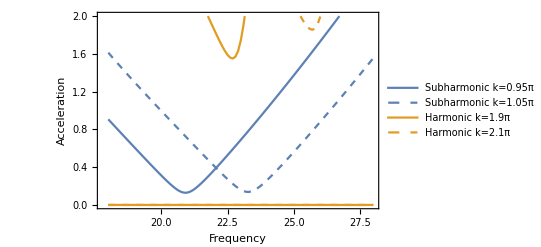

```mathematica
p=Legended[Show[ListPlot[Transpose[{freqs/(2*Pi),#}]&/@(Re[(Transpose[SortBy[#,Re[#]&]&/@subharmonic])]/980),PlotRange->{0,2},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]]}],ListPlot[Transpose[{freqs/(2*Pi),#}]&/@(Re[(Transpose[SortBy[#,Re[#]&]&/@subharmonic2])]/980),PlotRange->{0,2},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Dashed]}],ListPlot[Transpose[{freqs/(2*Pi),#}]&/@(Re[(Transpose[SortBy[#,Re[#]&]&/@harmonic])]/980),PlotRange->{0,2},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]]]}],ListPlot[Transpose[{freqs/(2*Pi),#}]&/@(Re[(Transpose[SortBy[#,Re[#]&]&/@harmonic2])]/980),PlotRange->{0,2},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Dashed]}]],LineLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[2]],Dashed]},{"Subharmonic k=0.95π","Subharmonic k=1.05π","Harmonic k=1.9π","Harmonic k=2.1π"}]]
```

```mathematica
Export["boundaries.pdf",p]
```

boundaries.pdf

### periodic

```mathematica
C1[m1_,m2_,n1_,n2_]:=ⅇ^(- h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]+ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]]
S1[m1_,m2_,n1_,n2_]:=-(ⅇ^(-h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]-ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]])
C2[l1_,m1_,m2_,n1_,n2_]:=ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]+ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]
S2[l1_,m1_,m2_,n1_,n2_]:=-(ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]-ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)])
κx[n1_,m1_]:=qx+n1*q1.{1,0}+m1*q2.{1,0}
κy[n1_,m1_]:=qy+n1*q1.{0,1}+m1*q2.{0,1}
κ1[n1_,m1_]:=(κx[n1,m1]^2+κy[n1,m1]^2)^(1/2)
Ω1[n1_,m1_,l1_]:=μ/ρ*(I*ρ/μ*(ω+l1*ωd)+κ1[n1,m1]^2)
mat1[n1_,n2_,m1_,m2_,l1_,l2_]:={{C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κx[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κy[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{ⅈ μ κx[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),ⅈ μ κy[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),1/2 (C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+κ1[n1,m1] (2 μ (-C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2]) κ1[n1,m1]+(S1[m1,m2,n1,n2] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))}} l1,l2
mat2[n1_,n2_,m1_,m2_,l1_,l2_]:=-{{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,(ρ^2 S1[m1,m2,n1,n2] κ1[n1,m1])/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))}} (-1/2 (-1+l1,l2+1+l1,l2))
```

```mathematica
FullSimplify[TrigToExp[((mat1[0,0,0,0,l1,l2]/.as->0)-(mat1flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}]))],ρ>0&&μ>0]
FullSimplify[TrigToExp[((mat2[0,0,0,0,l1,l2]/.as->0)-(mat2flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}]))],ρ>0&&μ>0]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
M=3;
M2=3;
ks=2*Pi;

Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]

freq=2*Pi*22;
subs={q1->ks*{3.^(1/2)/2,-1/2},q2->ks*{0,1}};

{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs1/.ωd->freq];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.ssubs1/.ωd->freq];

evalsbase
evalsbase2

Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1/.ωd->freq/.as->0.1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1/.ωd->freq/.as->0.1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];

w=lev[[All,-1]];
v=rev[[All,-1]];
(Conjugate[w].eq1.v)/(Conjugate[w].eq2.v)
```

{0.060676,Null}

{0.010202,Null}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-84409.2+211.425 ⅈ,84409.2-211.43 ⅈ,-22943.5+3.73057 ⅈ,22943.1-3.87004 ⅈ,363.837+0.00242976 ⅈ,-363.443+0.112272 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-84412.4-210.648 ⅈ,84410.3+211.271 ⅈ,22943.9+3.62789 ⅈ,-22943.8-3.38618 ⅈ,363.872-0.0543813 ⅈ,-363.839+0.00688678 ⅈ}

{301.64,Null}

{43.046,Null}

-363.834+6.77334×10^-6 ⅈ

```mathematica
ws={};
vs={};
λs={};
w=lev[[All,-1]];
v=rev[[All,-1]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].eq1.v/(Conjugate[w].eq2.v);
Print[k, " ", λ," ", Norm[eq1.v-λ*eq2.v]," ", Norm[Conjugate[Transpose[eq1]].w-Conjugate[λ*Transpose[eq2]].w]];
v=Quiet[LinearSolve[(λ*eq2-eq1),eq2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*eq2-eq1)]],Conjugate[Transpose[eq2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
```

1 -363.834+6.77334×10^-6 ⅈ 1.38634×10^10 6.50197

2 -391.654+0.000122984 ⅈ 2.62666×10^6 1.10932

3 -388.506+0.000340565 ⅈ 416.668 1.18842

4 -381.524+0.00054127 ⅈ 0.831907 0.810809

5 -377.043+0.0000587781 ⅈ 0.140558 0.168977

6 -376.898+4.27175×10^-9 ⅈ 0.000631754 0.000743927

7 -376.898+7.91786×10^-10 ⅈ 2.08327×10^-6 3.73916×10^-6

8 -376.898+7.9179×10^-10 ⅈ 3.29485×10^-6 3.7218×10^-6

9 -376.898+7.91744×10^-10 ⅈ 2.47168×10^-6 3.27608×10^-6

10 -376.898+7.91754×10^-10 ⅈ 2.79573×10^-6 3.63123×10^-6

{11.9407,Null}

```mathematica
(*subharmonic1*)
```

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{187.998,Null}

{24.7918,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
w=lev[[All,-1]];
v=rev[[All,-1]];
Do[
subs2={ωd->2*Pi*22,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,0.05,0.4,0.05}]
```

{19.7804,Null}{2.7462,Null}

1 -363.834+4.72154×10^-6 ⅈ 1.66596×10^8 2.62715

2 -373.862+6.06134×10^-7 ⅈ 10834. 0.07413

3 -373.816+5.46365×10^-10 ⅈ 0.00533848 0.000134707

4 -373.816+5.39593×10^-10 ⅈ 8.48346×10^-8 1.43702×10^-7

5 -373.816+5.39387×10^-10 ⅈ 1.0217×10^-7 1.50527×10^-7

6 -373.816+5.39629×10^-10 ⅈ 1.23131×10^-7 1.40756×10^-7

7 -373.816+5.39416×10^-10 ⅈ 6.55837×10^-8 1.60886×10^-7

8 -373.816+5.39529×10^-10 ⅈ 8.11457×10^-8 1.48024×10^-7

9 -373.816+5.39529×10^-10 ⅈ 9.58773×10^-8 1.48043×10^-7

10 -373.816+5.39359×10^-10 ⅈ 1.24835×10^-7 1.41749×10^-7

{20.358,Null}{2.93368,Null}

1 -392.908-2.33726×10^-10 ⅈ 4.8133×10^9 2.87443

2 -402.925-9.61916×10^-9 ⅈ 474779. 0.937271

3 -409.136-1.97488×10^-9 ⅈ 37.3516 0.276574

4 -409.705+8.43585×10^-10 ⅈ 0.00634085 0.00503457

5 -409.706+8.25807×10^-10 ⅈ 0.0000110723 3.02542×10^-6

6 -409.706+8.25736×10^-10 ⅈ 5.88223×10^-6 2.90871×10^-6

7 -409.706+8.25607×10^-10 ⅈ 6.98298×10^-6 3.30055×10^-6

8 -409.706+8.25608×10^-10 ⅈ 5.9768×10^-6 2.90941×10^-6

9 -409.706+8.25537×10^-10 ⅈ 0.000011391 3.19233×10^-6

10 -409.706+8.25651×10^-10 ⅈ 8.31244×10^-6 2.78591×10^-6

{21.9749,Null}{2.87209,Null}

1 -452.81-9.82469×10^-9 ⅈ 3.57289×10^10 3.8018

2 -468.006-3.13875×10^-9 ⅈ 3.28565×10^6 0.166438

3 -468.051+1.51238×10^-9 ⅈ 1.48541 0.000118841

4 -468.051+1.50922×10^-9 ⅈ 0.000147841 0.000116781

5 -468.051+1.50919×10^-9 ⅈ 0.000136796 0.0000869003

6 -468.051+1.50925×10^-9 ⅈ 0.000135557 0.000109282

7 -468.051+1.50949×10^-9 ⅈ 0.000192751 0.000104974

8 -468.051+1.50916×10^-9 ⅈ 0.00029518 0.0000991874

9 -468.051+1.50919×10^-9 ⅈ 0.000163847 0.000127609

10 -468.051+1.50918×10^-9 ⅈ 0.00022618 0.0000991389

{24.0452,Null}{3.00969,Null}

1 -542.728-3.09843×10^-8 ⅈ 1.81217×10^11 5.84705

2 -560.729+9.84073×10^-10 ⅈ 1.91152×10^7 0.0851591

3 -560.732+3.02236×10^-9 ⅈ 0.465774 0.00605367

4 -560.732+3.0029×10^-9 ⅈ 0.00187996 0.0064328

5 -560.732+2.99855×10^-9 ⅈ 0.00171715 0.00706782

6 -560.732+3.01259×10^-9 ⅈ 0.0013944 0.0057416

7 -560.732+2.98135×10^-9 ⅈ 0.00130558 0.00592594

8 -560.732+3.01949×10^-9 ⅈ 0.00254726 0.00679724

9 -560.732+2.97172×10^-9 ⅈ 0.00135508 0.00646694

10 -560.732+3.01659×10^-9 ⅈ 0.00142639 0.00610341

{28.3406,Null}{3.03122,Null}

1 -675.622-4.19095×10^-7 ⅈ 6.62432×10^11 1169.77

2 -701.027-4.64031×10^-7 ⅈ 9.79586×10^7 0.576368

3 -701.033-7.03949×10^-10 ⅈ 6.22917 0.958101

4 -701.033-1.09716×10^-9 ⅈ 0.0105078 0.501064

5 -701.033+7.68125×10^-10 ⅈ 0.00925912 0.905811

6 -701.033+2.96473×10^-9 ⅈ 0.00830499 0.892984

7 -701.033-1.10074×10^-9 ⅈ 0.00949777 0.766601

8 -701.033-3.49888×10^-9 ⅈ 0.0113572 1.27522

9 -701.033+9.99904×10^-10 ⅈ 0.00806228 1.14861

10 -701.033+9.31607×10^-10 ⅈ 0.0112416 0.652638

{29.0306,Null}{3.13777,Null}

1 -871.956-1.93977×10^-6 ⅈ 2.00765×10^12 3.98517×10^6

2 -914.046+0.000232778 ⅈ 4.81431×10^8 286.797

3 -914.067+7.23955×10^-8 ⅈ 104.503 240.996

4 -914.067+1.41721×10^-7 ⅈ 0.0934632 307.895

5 -914.067-2.32961×10^-7 ⅈ 0.113504 245.29

6 -914.067-1.85659×10^-7 ⅈ 0.0896577 1276.74

7 -914.067+1.72784×10^-7 ⅈ 0.128037 1184.38

8 -914.067-7.58371×10^-7 ⅈ 0.118553 351.524

9 -914.067+1.3629×10^-7 ⅈ 0.0748793 371.299

10 -914.067-1.44718×10^-7 ⅈ 0.0912256 2118.34

{27.7917,Null}{2.95572,Null}

1 -1165.23-0.00713421 ⅈ 5.18697×10^12 4.53387×10^9

2 -1248.02-0.0154534 ⅈ 1.3069×10^9 510.353

3 -1248.12-4.77225×10^-6 ⅈ 1247.8 1171.36

4 -1248.12+0.000019151 ⅈ 0.562519 9944.65

5 -1248.12+0.0000396849 ⅈ 0.267368 2196.12

6 -1248.12-0.0000291901 ⅈ 0.33491 341.367

7 -1248.12+0.0000469903 ⅈ 0.440256 1196.83

8 -1248.12-0.0000386622 ⅈ 0.319262 1330.12

9 -1248.12-0.0000447905 ⅈ 0.35564 2209.5

10 -1248.12-7.22967×10^-6 ⅈ 0.338242 2234.36

{28.2955,Null}{2.95882,Null}

1 -1634.19+0.0176702 ⅈ 6.29306×10^12 2.42544×10^11

2 -1815.24+2.30338 ⅈ 1.52776×10^9 55134.6

3 -1812.74-0.000246164 ⅈ 51901.2 51329.7

4 -1812.74-0.000319573 ⅈ 0.538596 113776.

5 -1812.74+0.000686324 ⅈ 0.721073 189795.

6 -1812.74-0.000894367 ⅈ 0.444788 153901.

7 -1812.74-0.000698579 ⅈ 0.541107 13757.8

8 -1812.74-0.0000478696 ⅈ 0.515564 64824.8

9 -1812.74-0.000742591 ⅈ 0.557215 65168.3

10 -1812.74-0.00126009 ⅈ 0.712486 125101.

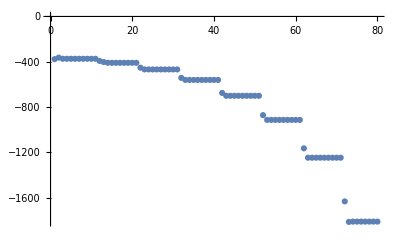

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λps={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->0.4};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λps,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,2*Pi*22,2*Pi*28,2*Pi}]]
```

{28.7492,Null}{2.949,Null}

1 -1812.74-0.00126009 ⅈ 0.712486 125101.

2 -1812.74-0.000181211 ⅈ 0.63333 1.69194×10^6

3 -1812.74-0.000616865 ⅈ 0.583149 97928.1

4 -1812.74-0.000862085 ⅈ 0.523231 51931.6

5 -1812.74+0.000274281 ⅈ 0.973062 114017.

6 -1812.74-0.0013541 ⅈ 0.702249 1.10733×10^6

7 -1812.74-0.000560651 ⅈ 0.612575 33293.4

8 -1812.74+0.00026626 ⅈ 0.55885 65367.3

9 -1812.74+0.000359093 ⅈ 0.848393 44143.5

10 -1812.74-0.0000610532 ⅈ 0.768709 48465.2

{27.7802,Null}{2.99559,Null}

1 -2247.42+0.404261 ⅈ 1.14464×10^6 1.20904×10^19

2 -2247.78+0.0000335835 ⅈ 7.92607 1.36607×10^6

3 -2247.78+0.00298475 ⅈ 0.714726 1.2431×10^6

4 -2247.78+0.00128407 ⅈ 0.676549 2.21616×10^6

5 -2247.77-0.00150019 ⅈ 0.465997 1.70928×10^6

6 -2247.79-0.0226867 ⅈ 0.925818 1.15006×10^7

7 -2247.78+0.000184042 ⅈ 0.448191 1.07495×10^6

8 -2247.77+0.00195604 ⅈ 0.534138 1.91445×10^7

9 -2247.78-0.000367449 ⅈ 0.745695 4.3383×10^6

10 -2247.77+0.000988542 ⅈ 0.506319 4.85447×10^6

{27.1041,Null}{2.97389,Null}

1 -2696.03+0.781279 ⅈ 882146. 7.49709×10^20

2 -2692.53+0.00656296 ⅈ 31.622 8.86554×10^6

3 -2692.53-0.00209884 ⅈ 0.440651 2.31612×10^6

4 -2692.53+0.00619972 ⅈ 0.569891 656468.

5 -2692.54+0.000554959 ⅈ 0.441124 3.14643×10^6

6 -2692.54-0.000615939 ⅈ 0.421087 7.88353×10^6

7 -2692.53+0.00387954 ⅈ 0.558908 3.27969×10^7

8 -2692.53-0.00336738 ⅈ 0.49053 4.32174×10^6

9 -2692.53-0.00248132 ⅈ 0.726208 1.63749×10^6

10 -2692.54+0.00366782 ⅈ 0.385579 1.81018×10^6

{25.8299,Null}{2.97275,Null}

1 -3162.13+0.741292 ⅈ 578147. 4.59429×10^20

2 -3158.16+0.00248653 ⅈ 18.5036 4.50959×10^6

3 -3158.17+0.00499614 ⅈ 0.651638 1.79642×10^7

4 -3158.19+0.0108571 ⅈ 0.560723 2.70241×10^6

5 -3158.18-0.00272955 ⅈ 0.794313 8.65984×10^6

6 -3158.16-0.0370368 ⅈ 0.779245 4.74929×10^6

7 -3158.16-0.00189185 ⅈ 0.69682 9.29388×10^7

8 -3158.18+0.00530139 ⅈ 0.446246 2.84898×10^7

9 -3158.17+0.0133185 ⅈ 0.58321 8.06823×10^6

10 -3158.16+0.00996923 ⅈ 0.641359 1.68954×10^7

{26.4728,Null}{2.93076,Null}

1 -3648.65-3.27287 ⅈ 386438. 6.54093×10^20

2 -3633.93-0.0281925 ⅈ 66.2339 2.67626×10^7

3 -3634.04-0.00644839 ⅈ 0.613023 1.47802×10^7

4 -3634.05-0.00429817 ⅈ 0.697155 7.2254×10^7

5 -3634.06-0.00259409 ⅈ 0.725955 5.0669×10^7

6 -3634.04+0.00457737 ⅈ 0.71563 2.66916×10^7

7 -3634.04-0.0158863 ⅈ 1.10685 2.04135×10^7

8 -3634.04+0.00606464 ⅈ 0.501653 1.0941×10^7

9 -3634.15-0.0422862 ⅈ 0.828217 2.38322×10^8

10 -3634.06+0.00309469 ⅈ 0.816824 1.95268×10^7

{25.2964,Null}{2.96632,Null}

1 -4090.31+28.8094 ⅈ 191372. 1.57483×10^21

2 -4003.96+7.61697 ⅈ 296.131 4.88484×10^6

3 -3982.11+2.20544 ⅈ 21.364 1.98521×10^7

4 -3984.45-0.00669827 ⅈ 1.65566 3.83452×10^6

5 -3984.4-0.0218133 ⅈ 1.82206 1.3937×10^7

6 -3984.42-0.00880909 ⅈ 1.13481 3.35941×10^7

7 -3984.46-0.00572063 ⅈ 1.75313 1.8738×10^7

8 -3984.46-0.0315313 ⅈ 1.32029 8.35254×10^6

9 -3984.46-0.0260336 ⅈ 1.30255 6.12248×10^6

10 -3984.48-0.0178818 ⅈ 1.05436 3.74053×10^7

{25.2114,Null}{2.95692,Null}

1 -4242.51-67.2576 ⅈ 324582. 2.0673×10^21

2 -4070.3+709.063 ⅈ 5969.58 1.74055×10^6

3 -3938.47-66.7848 ⅈ 3430.35 2.40066×10^6

4 -3687.14+52.4058 ⅈ 1891.79 4.35538×10^6

5 -3686.51+3.27161 ⅈ 98.0256 6.11322×10^6

6 -3683.44-0.0966141 ⅈ 3.6116 1.05624×10^7

7 -3683.4-0.0165685 ⅈ 2.44331 955317.

8 -3683.41-0.0469111 ⅈ 3.44068 3.49451×10^6

9 -3683.39-0.00849495 ⅈ 2.29997 4.88683×10^6

10 -3683.41+0.00780927 ⅈ 3.46924 1.70054×10^6

{392.421,Null}

```mathematica
w=w0;
v=v0;
λms={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->0.4};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λms,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,2*Pi*22,2*Pi*18,-2*Pi}]]
```

{28.2739,Null}{2.96851,Null}

1 -1812.74-0.00126009 ⅈ 0.712486 125101.

2 -1812.74-0.000181211 ⅈ 0.63333 1.69194×10^6

3 -1812.74-0.000616865 ⅈ 0.583149 97928.1

4 -1812.74-0.000862085 ⅈ 0.523231 51931.6

5 -1812.74+0.000274281 ⅈ 0.973062 114017.

6 -1812.74-0.0013541 ⅈ 0.702249 1.10733×10^6

7 -1812.74-0.000560651 ⅈ 0.612575 33293.4

8 -1812.74+0.00026626 ⅈ 0.55885 65367.3

9 -1812.74+0.000359093 ⅈ 0.848393 44143.5

10 -1812.74-0.0000610532 ⅈ 0.768709 48465.2

{28.177,Null}{2.99819,Null}

1 -1390.85-0.374819 ⅈ 822507. 7.95883×10^17

2 -1396.65-0.000204581 ⅈ 117.205 6917.84

3 -1396.65+0.00027743 ⅈ 0.475989 9875.12

4 -1396.65-0.0001863 ⅈ 0.347312 33782.1

5 -1396.65+0.000230758 ⅈ 0.529079 13596.4

6 -1396.65+0.000241298 ⅈ 0.393402 14466.5

7 -1396.65-0.000271947 ⅈ 0.477835 8764.71

8 -1396.65+0.000484185 ⅈ 0.506906 13382.8

9 -1396.65+0.000231186 ⅈ 0.561983 6350.25

10 -1396.65+0.000338775 ⅈ 0.527752 9973.58

{28.3635,Null}{2.9467,Null}

1 -1001.24-0.00479077 ⅈ 901465. 1.49464×10^18

2 -1012.8+0.000191358 ⅈ 249.922 683.724

3 -1012.81+0.0000702902 ⅈ 0.296235 554.15

4 -1012.81+0.0000893405 ⅈ 0.32536 1206.76

5 -1012.81-0.0000631469 ⅈ 0.220275 1174.06

6 -1012.81+0.000060828 ⅈ 0.482334 1173.57

7 -1012.81+0.0000382578 ⅈ 0.411014 237.806

8 -1012.81-0.0000932345 ⅈ 0.484769 1141.9

9 -1012.81+0.000052882 ⅈ 0.418583 428.368

10 -1012.81-4.45969×10^-6 ⅈ 0.302408 725.677

{28.9653,Null}{2.96739,Null}

1 -659.145-0.000238047 ⅈ 863448. 7.3754×10^15

2 -633.185+0.0000134309 ⅈ 421.318 741.162

3 -632.219-3.68544×10^-6 ⅈ 0.526288 626.587

4 -632.219-6.84024×10^-6 ⅈ 0.239132 515.606

5 -632.219-4.65057×10^-6 ⅈ 0.540383 405.025

6 -632.219-0.0000413772 ⅈ 0.392011 2104.84

7 -632.219-5.47841×10^-6 ⅈ 0.312744 478.648

8 -632.219-0.0000108776 ⅈ 0.266488 526.436

9 -632.219-7.36764×10^-6 ⅈ 0.307016 903.78

10 -632.219-0.0000134066 ⅈ 0.32806 2183.11

{28.841,Null}{2.95422,Null}

1 -378.238+0.0000159783 ⅈ 640895. 2.34526×10^16

2 -400.576+0.0000130856 ⅈ 498.489 61.9304

3 -400.596+0.0000118947 ⅈ 0.229355 107.692

4 -400.596+5.49248×10^-6 ⅈ 0.287829 242.162

5 -400.596-2.47455×10^-6 ⅈ 0.411753 572.502

6 -400.596+7.45506×10^-6 ⅈ 0.392318 37.8827

7 -400.596-2.63541×10^-6 ⅈ 0.249615 69.6616

8 -400.596+1.41013×10^-6 ⅈ 0.345733 235.253

9 -400.596-8.31104×10^-6 ⅈ 0.25993 155.668

10 -400.596+4.07883×10^-6 ⅈ 0.117377 25.934

{290.378,Null}

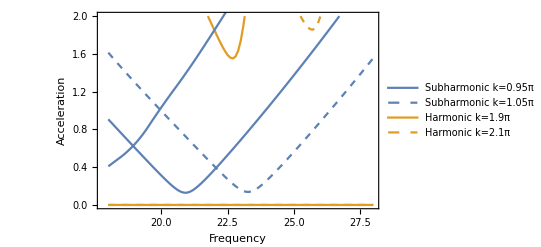

```mathematica
Show[p,ListPlot[Join[Reverse[Transpose[{Table[Freq/(2*Pi),{Freq,2*Pi*22,2*Pi*18,-2*Pi}],-Re[λms][[10;;-1;;10]]/980}]][[1;;-2]],Transpose[{Table[Freq/(2*Pi),{Freq,2*Pi*22,2*Pi*28,2*Pi}],-Re[λps][[10;;-1;;10]]/980}]],Joined->True,InterpolationOrder->2]]
```

```mathematica
(*subharmonic2*)
```

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{190.329,Null}

{26.2026,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
w=lev[[All,-1]];
v=rev[[All,-1]];
Do[
subs2={ωd->2*Pi*22,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,0.05,0.4,0.05}]
```

{20.2365,Null}{2.96117,Null}

1 290.74-0.0120201 ⅈ 2.02728×10^8 5.49775×10^7

2 393.908-0.0010475 ⅈ 141559. 3.53418

3 397.485-0.0000232465 ⅈ 5.51813 0.0731293

4 397.522-1.16793×10^-9 ⅈ 0.000102601 0.000109562

5 397.522-9.98746×10^-10 ⅈ 9.79902×10^-8 2.84678×10^-7

6 397.522-9.9908×10^-10 ⅈ 1.54953×10^-7 2.36436×10^-7

7 397.522-9.98853×10^-10 ⅈ 1.07201×10^-7 2.60029×10^-7

8 397.522-9.98938×10^-10 ⅈ 1.46154×10^-7 2.78972×10^-7

9 397.522-9.98597×10^-10 ⅈ 1.58666×10^-7 3.00396×10^-7

10 397.522-9.98881×10^-10 ⅈ 2.51735×10^-7 2.74158×10^-7

{22.1252,Null}{2.92928,Null}

1 387.985-4.27576×10^-10 ⅈ 5.66661×10^9 2.68345

2 378.654-7.61418×10^-11 ⅈ 408824. 0.532151

3 376.903-6.58844×10^-10 ⅈ 7.47208 0.0329968

4 376.897-7.91715×10^-10 ⅈ 0.000011796 6.90586×10^-6

5 376.897-7.91751×10^-10 ⅈ 9.22186×10^-6 3.74174×10^-6

6 376.897-7.91829×10^-10 ⅈ 0.0000127779 3.72882×10^-6

7 376.897-7.91601×10^-10 ⅈ 0.0000151828 3.35613×10^-6

8 376.897-7.918×10^-10 ⅈ 0.0000150587 3.90211×10^-6

9 376.897-7.91395×10^-10 ⅈ 9.03858×10^-6 4.1887×10^-6

10 376.897-7.91772×10^-10 ⅈ 0.0000151884 3.67242×10^-6

{22.0643,Null}{2.96793,Null}

1 355.945+3.37387×10^-9 ⅈ 5.22579×10^10 2.97858

2 347.904+2.25188×10^-9 ⅈ 2.41921×10^6 0.0916996

3 347.892-5.60291×10^-10 ⅈ 0.298585 0.0000634212

4 347.892-5.60135×10^-10 ⅈ 0.0000891262 0.0000693849

5 347.892-5.59936×10^-10 ⅈ 0.00018316 0.0000674652

6 347.892-5.59375×10^-10 ⅈ 0.00016408 0.0000541621

7 347.892-5.60078×10^-10 ⅈ 0.000160151 0.0000725697

8 347.892-5.59766×10^-10 ⅈ 0.000166757 0.0000700421

9 347.892-5.5951×10^-10 ⅈ 0.000148791 0.000058594

10 347.892-5.5968×10^-10 ⅈ 0.000198991 0.0000775978

{24.1721,Null}{3.0095,Null}

1 313.122+1.28824×10^-8 ⅈ 2.82064×10^11 4.61054

2 306.324+2.25711×10^-10 ⅈ 1.08063×10^7 0.0293676

3 306.324-3.36847×10^-10 ⅈ 0.00241392 0.0010675

4 306.324-3.34055×10^-10 ⅈ 0.00279855 0.00102034

5 306.324-3.29358×10^-10 ⅈ 0.00330942 0.00129511

6 306.324-3.25244×10^-10 ⅈ 0.00198026 0.00123921

7 306.324-3.281×10^-10 ⅈ 0.00233697 0.00124299

8 306.324-3.32136×10^-10 ⅈ 0.00376657 0.00160531

9 306.324-3.23752×10^-10 ⅈ 0.00338566 0.0014094

10 306.324-3.32307×10^-10 ⅈ 0.00297892 0.00137299

{27.9572,Null}{3.01707,Null}

1 260.81-1.59534×10^-8 ⅈ 1.18192×10^12 226.818

2 254.571+1.37561×10^-9 ⅈ 4.13307×10^7 0.0524953

3 254.571-5.94582×10^-10 ⅈ 0.173419 0.0422647

4 254.571+8.0334×10^-11 ⅈ 0.0126492 0.0197602

5 254.571-3.19275×10^-10 ⅈ 0.0227803 0.043911

6 254.571-3.71273×10^-10 ⅈ 0.0199642 0.0170548

7 254.571-6.31104×10^-11 ⅈ 0.0182419 0.0663775

8 254.571-7.01448×10^-11 ⅈ 0.0253391 0.0803787

9 254.571-6.33193×10^-10 ⅈ 0.0180042 0.0532077

10 254.571-1.76317×10^-9 ⅈ 0.0136862 0.038363

{28.5184,Null}{3.02003,Null}

1 205.275+4.1797×10^-10 ⅈ 4.30566×10^12 263716.

2 201.215-1.15077×10^-8 ⅈ 9.60075×10^7 44.418

3 201.216-7.02357×10^-9 ⅈ 0.832291 4.07741

4 201.216-2.56042×10^-8 ⅈ 0.272066 1.02514

5 201.216+1.1719×10^-8 ⅈ 0.100876 1.21341

6 201.216+1.21502×10^-8 ⅈ 0.141012 0.577288

7 201.216+6.95275×10^-9 ⅈ 0.131716 1.85254

8 201.216-2.98863×10^-8 ⅈ 0.0407101 1.90536

9 201.216+8.27315×10^-9 ⅈ 0.0887932 6.79171

10 201.216-3.2787×10^-8 ⅈ 0.15531 10.1199

{28.6225,Null}{3.11536,Null}

1 168.595-1.32778×10^-6 ⅈ 1.39986×10^13 1.36801×10^7

2 177.027-1.99115×10^-6 ⅈ 3.01258×10^8 1.86168

3 177.044+6.35236×10^-8 ⅈ 53.3376 8.87119

4 177.044-5.76747×10^-8 ⅈ 0.424431 4.38768

5 177.044+3.10836×10^-7 ⅈ 0.344393 2.51587

6 177.044-7.92681×10^-8 ⅈ 0.337007 17.4387

7 177.044+1.08894×10^-6 ⅈ 0.326612 66.8036

8 177.044+7.40972×10^-7 ⅈ 0.437084 2.358

9 177.044-4.16485×10^-9 ⅈ 0.406851 15.6728

10 177.044-1.46828×10^-7 ⅈ 0.442719 9.65909

{28.1894,Null}{2.94551,Null}

1 177.999-0.0000235673 ⅈ 1.9247×10^13 2.83396×10^9

2 235.124+0.0000264499 ⅈ 1.34384×10^9 51.8274

3 236.009-0.0000100021 ⅈ 11941.3 1838.74

4 236.009-0.0000145368 ⅈ 0.433307 183.011

5 236.009+1.21248×10^-6 ⅈ 0.350733 158.63

6 236.009+5.41882×10^-6 ⅈ 0.379427 84.0274

7 236.009+8.06373×10^-6 ⅈ 0.203957 299.726

8 236.009-2.03739×10^-6 ⅈ 0.474261 106.002

9 236.009+1.78397×10^-7 ⅈ 0.445563 198.534

10 236.009+9.47073×10^-6 ⅈ 0.618471 153.222

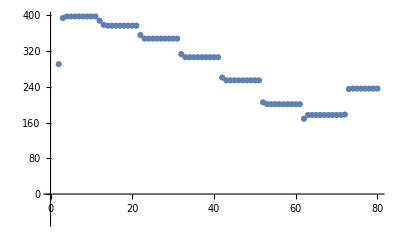

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λps2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->0.4};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λps2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,2*Pi*22,2*Pi*28,2*Pi}]]
```

{28.2544,Null}{2.97217,Null}

1 236.009+9.47073×10^-6 ⅈ 0.618471 153.222

2 236.009-0.00001185 ⅈ 0.531348 5467.85

3 236.009+3.85407×10^-6 ⅈ 0.49339 88.4451

4 236.009+9.54646×10^-6 ⅈ 0.445997 130.265

5 236.009+7.80014×10^-7 ⅈ 0.524319 448.954

6 236.009-0.0000118017 ⅈ 0.23134 271.265

7 236.009-6.81188×10^-6 ⅈ 0.321626 117.068

8 236.009+7.852×10^-6 ⅈ 0.173934 1115.12

9 236.009-3.29442×10^-6 ⅈ 0.427167 1312.97

10 236.009-2.60571×10^-6 ⅈ 0.232717 3824.36

{27.5634,Null}{2.96415,Null}

1 417.794+0.0000248779 ⅈ 560109. 1.00221×10^17

2 496.531+0.000726978 ⅈ 812.465 1996.96

3 497.186+0.0000554395 ⅈ 0.455097 34152.1

4 497.186+0.000070541 ⅈ 0.290467 20888.3

5 497.186-0.000057897 ⅈ 0.424784 1.46206×10^6

6 497.186-0.000030919 ⅈ 0.266594 17104.5

7 497.186+0.0000213633 ⅈ 0.334225 30640.5

8 497.186-0.0000166201 ⅈ 0.403923 4731.71

9 497.186-0.0000830123 ⅈ 0.445703 5011.37

10 497.186-6.54224×10^-6 ⅈ 0.459273 4385.19

{27.055,Null}{3.09523,Null}

1 807.723-0.00505902 ⅈ 448435. 1.98163×10^18

2 813.257+0.000983681 ⅈ 21.2459 165346.

3 813.257-0.00023929 ⅈ 0.272265 93235.9

4 813.258-0.00128478 ⅈ 0.319307 237477.

5 813.256+0.0000608516 ⅈ 0.26064 64226.4

6 813.257+0.000240287 ⅈ 0.336369 83353.3

7 813.257-0.000136445 ⅈ 0.285138 48539.

8 813.256-0.000563998 ⅈ 0.436504 240044.

9 813.258+0.000202384 ⅈ 0.279616 129155.

10 813.256+0.000228167 ⅈ 0.247369 65742.4

{26.0037,Null}{2.97576,Null}

1 1152.01-0.0124044 ⅈ 279946. 4.41242×10^19

2 1149.72-0.000318577 ⅈ 2.97984 549349.

3 1149.72+0.000445025 ⅈ 0.410274 1.35206×10^6

4 1149.72+0.000363332 ⅈ 0.378803 850807.

5 1149.72+0.000559753 ⅈ 0.21685 302801.

6 1149.72+0.000193627 ⅈ 0.285372 974438.

7 1149.72+0.00038993 ⅈ 0.226372 325590.

8 1149.72+0.000401502 ⅈ 0.22137 318471.

9 1149.72-0.000880657 ⅈ 0.256818 219009.

10 1149.72+0.000301138 ⅈ 0.370828 1.02038×10^6

{26.152,Null}{2.94709,Null}

1 1500.75-1.23066 ⅈ 196519. 3.11089×10^20

2 1502.+0.000229311 ⅈ 4.95214 1.69458×10^6

3 1502.+0.0000321278 ⅈ 0.27449 534756.

4 1502.-0.00237412 ⅈ 0.344647 2.51349×10^6

5 1502.-0.000114669 ⅈ 0.489569 419823.

6 1502.-0.000820537 ⅈ 0.471116 6.93254×10^6

7 1502.+0.000594117 ⅈ 0.243383 358326.

8 1502.-0.000092095 ⅈ 0.374497 1.11336×10^6

9 1502.-0.000878497 ⅈ 0.390314 589751.

10 1502.+0.000304564 ⅈ 0.278093 3.64528×10^6

{25.7124,Null}{2.97286,Null}

1 1872.74+0.400064 ⅈ 169332. 4.89947×10^20

2 1870.59+0.00101337 ⅈ 5.64743 1.17532×10^7

3 1870.59-0.00171555 ⅈ 0.507836 1.8996×10^7

4 1870.59+0.000180497 ⅈ 0.69043 6.4971×10^6

5 1870.59+0.00015566 ⅈ 0.624621 2.68969×10^7

6 1870.59-0.000218527 ⅈ 0.598856 5.54873×10^6

7 1870.59-0.000530462 ⅈ 0.542987 1.99835×10^7

8 1870.59+0.00320537 ⅈ 0.670571 1.43474×10^7

9 1870.59+0.000381434 ⅈ 0.685669 5.40608×10^6

10 1870.59-0.000258463 ⅈ 1.09589 4.02131×10^6

{25.8112,Null}{2.975,Null}

1 2250.53+0.0153308 ⅈ 207329. 1.3115×10^22

2 2248.87-0.00610198 ⅈ 2.63702 1.11098×10^7

3 2248.86-0.00289319 ⅈ 1.32995 5.40184×10^6

4 2248.86+0.0012471 ⅈ 0.923089 1.58482×10^6

5 2248.87+0.00394355 ⅈ 1.49484 872547.

6 2248.87-0.00228941 ⅈ 1.38721 3.93563×10^6

7 2248.86-0.000235377 ⅈ 0.962258 4.96535×10^6

8 2248.86+0.00342987 ⅈ 0.858503 4.57121×10^6

9 2248.86+0.00714736 ⅈ 1.29016 2.57182×10^6

10 2248.87-0.00128137 ⅈ 0.88199 5.53091×10^6

{393.64,Null}

```mathematica
w=w0;
v=v0;
λms2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->0.4};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λms2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,2*Pi*22,2*Pi*18,-2*Pi}]]
```

{28.7075,Null}{2.97796,Null}

1 236.009+9.47073×10^-6 ⅈ 0.618471 153.222

2 236.009-0.00001185 ⅈ 0.531348 5467.85

3 236.009+3.85407×10^-6 ⅈ 0.49339 88.4451

4 236.009+9.54646×10^-6 ⅈ 0.445997 130.265

5 236.009+7.80014×10^-7 ⅈ 0.524319 448.954

6 236.009-0.0000118017 ⅈ 0.23134 271.265

7 236.009-6.81188×10^-6 ⅈ 0.321626 117.068

8 236.009+7.852×10^-6 ⅈ 0.173934 1115.12

9 236.009-3.29442×10^-6 ⅈ 0.427167 1312.97

10 236.009-2.60571×10^-6 ⅈ 0.232717 3824.36

{27.839,Null}{2.98466,Null}

1 61.4758-0.0000309014 ⅈ 408436. 6.58948×10^15

2 161.772-0.0000783894 ⅈ 3293.5 51.2935

3 262.638+6.39062×10^-6 ⅈ 1007.88 23.1119

4 271.266+3.24544×10^-6 ⅈ 16.306 18.1716

5 271.269-9.6454×10^-6 ⅈ 0.38485 833.909

6 271.268+1.81667×10^-6 ⅈ 0.258077 35.9317

7 271.268+5.06657×10^-6 ⅈ 0.298714 50.7057

8 271.269-8.57733×10^-6 ⅈ 0.47067 24.0427

9 271.268-8.96113×10^-6 ⅈ 0.281382 38.8366

10 271.268+0.0000129209 ⅈ 0.382143 33.0473

{28.2932,Null}{2.95121,Null}

1 482.3-0.0000724351 ⅈ 419421. 6.09301×10^14

2 532.208+0.0000445017 ⅈ 525.485 23.2847

3 532.303+2.5072×10^-7 ⅈ 0.322425 46.0325

4 532.303-0.0000540648 ⅈ 0.333828 54.4934

5 532.303-4.60654×10^-7 ⅈ 0.471708 28.5906

6 532.303-0.0000824987 ⅈ 0.360847 178.478

7 532.303-0.0000476189 ⅈ 0.251393 17.7849

8 532.303+0.0000231425 ⅈ 0.26294 37.9734

9 532.303-0.000026676 ⅈ 0.247866 37.1453

10 532.303-0.0000316022 ⅈ 0.357284 33.7432

{28.6905,Null}{2.96389,Null}

1 801.235-0.0000662994 ⅈ 337807. 4.37603×10^14

2 856.398-0.000114152 ⅈ 383.103 852.887

3 864.415-0.0000397562 ⅈ 25.9985 2548.39

4 864.425-0.0000203526 ⅈ 0.334642 661.097

5 864.425+0.000171599 ⅈ 0.345934 1428.75

6 864.426+0.0000582493 ⅈ 0.334919 360.168

7 864.426-0.0000510816 ⅈ 0.452379 948.435

8 864.425+0.0000663222 ⅈ 0.438668 479.681

9 864.425-0.0000405343 ⅈ 0.444176 352.799

10 864.425+0.0000165234 ⅈ 0.314204 1164.19

{28.4171,Null}{2.97056,Null}

1 1097.96-0.000858536 ⅈ 449660. 5.3626×10^16

2 1154.1+0.000322969 ⅈ 616.821 1068.07

3 1154.35+0.000227381 ⅈ 0.307208 2600.04

4 1154.35+0.0000733358 ⅈ 0.391051 183.455

5 1154.35+0.000189563 ⅈ 0.330099 628.303

6 1154.35+0.000044828 ⅈ 0.39432 159.619

7 1154.35+0.000147518 ⅈ 0.408289 197.42

8 1154.35-0.0000603005 ⅈ 0.367528 398.921

9 1154.35+0.0000212165 ⅈ 0.360021 838.809

10 1154.35+0.00023964 ⅈ 0.363814 945.027

{290.169,Null}

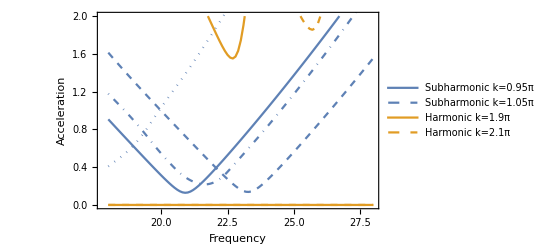

```mathematica
Show[p,ListPlot[Join[Reverse[Transpose[{Table[Freq/(2*Pi),{Freq,2*Pi*22,2*Pi*18,-2*Pi}],-Re[λms][[10;;-1;;10]]/980}]][[1;;-2]],Transpose[{Table[Freq/(2*Pi),{Freq,2*Pi*22,2*Pi*28,2*Pi}],-Re[λps][[10;;-1;;10]]/980}]],Joined->True,PlotStyle->Directive[Dotted],InterpolationOrder->2],ListPlot[Join[Reverse[Transpose[{Table[Freq/(2*Pi),{Freq,2*Pi*22,2*Pi*18,-2*Pi}],Re[λms2][[10;;-1;;10]]/980}]][[1;;-2]],Transpose[{Table[Freq/(2*Pi),{Freq,2*Pi*22,2*Pi*28,2*Pi}],Re[λps2][[10;;-1;;10]]/980}]],Joined->True,PlotStyle->Directive[DotDashed],InterpolationOrder->2]]
```